```mathematica
v={{{1},{0}},{{0},{1}}};
vl=1/(√2){ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[v[[1]],v[[1]],v[[1]],v[[1]]]+TensorProduct[v[[2]],v[[2]],v[[2]],v[[2]]]]]],ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[v[[1]],v[[1]],v[[2]],v[[2]]]+TensorProduct[v[[2]],v[[2]],v[[1]],v[[1]]]]]]};(* the codewords*)
P = Sum[vl[[i]].ConjugateTranspose[vl[[i]]], {i, 1, 2}]; (*The code space projector *)
```

```mathematica
base={P,vl[[1]].Transpose[vl[[2]]]+vl[[2]].Transpose[vl[[1]]],-ⅈ vl[[1]].Transpose[vl[[2]]]+ ⅈ vl[[2]].Transpose[vl[[1]]],vl[[1]].Transpose[vl[[1]]]-vl[[2]].Transpose[vl[[2]]]}; (* Subscript[I, C], Subscript[σ, x],Subscript[σ, y],Subscript[σ, z]. Here the Subscript[I, c] and the Subscript[σ, i] s are the logical operators. *)
```

```mathematica
Series[√(1-g),{g,0,3}]//Normal
```

1-g/2-g^2/8-g^3/16

```mathematica
A[g_]:={{{1,0},{0,√(1-g)}},{{0,√g},{0,0}}};
```

```mathematica
A1[g_]:={{{1,0},{0,1}},{{0,√g},{0,0}}};
```

```mathematica
B[g_,i_,j_,k_,l_]:=KroneckerProduct[A[g][[i]],A[g][[j]],A[g][[k]],A[g][[l]]](* Kraus operators for the Four-qubit codes Subscript[A, i] ⊗ Subscript[A, j] ⊗Subscript[A, k] ⊗ Subscript[A, l]*)
```

```mathematica
(*B1[g_,i_,j_,k_,l_]:=KroneckerProduct[A1[g][[i]],A1[g][[j]],A1[g][[k]],A1[g][[l]]]*)
```

```mathematica
Bn=Table[Subscript[bb, n,t],{n,16},{t,101}];


Table[For[i=1,i<=2,i++,
For[j=1,j<=2,j++,
For[k=1,k<=2,k++,
For[l=1,l<=2,l++,
n=2^3i+2^2 j + 2^1 k + l-14;
Bn[[n,t]]=B[t/100-0.01,i,j,k,l];
Bn1[[n,t]]=B1[t/100-0.01,i,j,k,l];
]]]],{t,101}];
```

```mathematica
Ep=ParallelTable[Sum[Bn[[n,t]].P.ConjugateTranspose[Bn[[n,t]]],{n,1,16}],{t,101}];(* ℰ(P)*)
```

```mathematica
Epc=ParallelTable[PseudoInverse[MatrixPower[Ep[[g]],0.5]],{g,101}];(* ℰ(P)^(-1/2)*)
```

```mathematica
R=ParallelTable[P.ConjugateTranspose[Bn[[n,t]]].Epc[[t]],{n,1,16},{t,101}];(*the kraus operators for the Petz*)
```

```mathematica
rhoI=ParallelTable[Sum[Bn[[n,t]].base[[1]].ConjugateTranspose[Bn[[n,t]]],{n,1,16}],{t,101}]; (*ℰ(Subscript[σ, i])*)
rhox=ParallelTable[Sum[Bn[[n,t]].base[[2]].ConjugateTranspose[Bn[[n,t]]],{n,1,16}],{t,101}];
rhoy=ParallelTable[Sum[Bn[[n,t]].base[[3]].ConjugateTranspose[Bn[[n,t]]],{n,1,16}],{t,101}];
rhoz=ParallelTable[Sum[Bn[[n,t]].base[[4]].ConjugateTranspose[Bn[[n,t]]],{n,1,16}],{t,101}];
```

```mathematica
(*(ℛ ◦ ℰ )[Subscript[σ, i]] here we fixed the recovery strength*)
```

```mathematica
recI=ParallelTable[Sum[R[[n,2]].rhoI[[t]].ConjugateTranspose[R[[n,2]]],{n,1,16}],{t,101}];
```

```mathematica
recx=ParallelTable[Sum[R[[n,2]].rhox[[t]].ConjugateTranspose[R[[n,2]]],{n,1,16}],{t,101}];
```

```mathematica
recy=ParallelTable[Sum[R[[n,2]].rhoy[[t]].ConjugateTranspose[R[[n,2]]],{n,1,16}],{t,101}];
```

```mathematica
recz=ParallelTable[Sum[R[[n,2]].rhoz[[t]].ConjugateTranspose[R[[n,2]]],{n,1,16}],{t,101}];
```

```mathematica
rec=Table[{recI[[t]],recx[[t]],recy[[t]],recz[[t]]},{t,101}];
```

```mathematica
M=ParallelTable[Table[1/2 Tr[base[[i]].rec[[t]][[j]]],{i,1,4},{j,1,4}],{t,101}];
```

```mathematica
r={{1},{x},{y},{z}};
```

```mathematica
fid=ParallelTable[Flatten[Transpose[r].Round[M[[t]],0.0001].r][[1]],{t,101}];
```

```mathematica
wcf=ParallelTable[{t/100-0.01,0.5NMinimize[{fid[[t]],x^2+y^2+z^2==1},{x,y,z},Method->{"SimulatedAnnealing"}][[1]]},{t,101}];
```

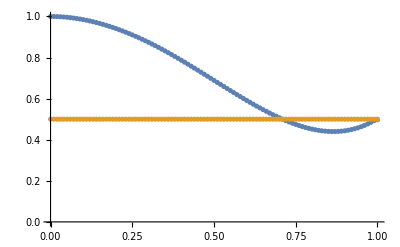

```mathematica
ListPlot[{wcf,Table[{i,0.5},{i,0,1,0.01}]},PlotRange->{{0,1},{0,1}}](*Here the x axis is the damping strength and the y axis is the worst-case fidelity *)
```

```mathematica
FindFit[Table[{0.01 t-0.01,wcf[[t,2]]},{t,31}],1- a x - b x^2- c x^3- d x^4- e x^5- f x^6,{a,b,c,d,e,f},x]
```

{a→0.000710834,b→1.60035,c→-0.694665,d→0.387593,e→-1.94225,f→3.00026}

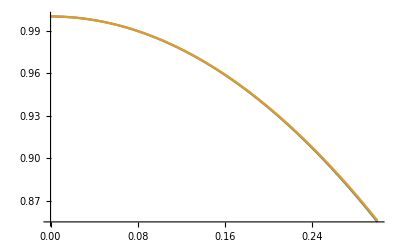

```mathematica
Plot[{1-1.61 x^2,1-1.6 x^2},{x,0,0.3}]
```

```mathematica
Table[Max[Eigenvalues[Sum[ConjugateTranspose[R[[i,t]]].R[[i,t]],{i,1,16}]]],{t,1,31}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
R1=SingularValueDecomposition[R[[1,2]]][[1]].SingularValueDecomposition[R[[1,2]]][[2]].ConjugateTranspose[SingularValueDecomposition[R[[1,2]]][[1]]];
```

```mathematica
R1//MatrixForm
```

(0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.495074 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.495074 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.495074 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.495074 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5)